```mathematica
expr=Cos[x y+Cos[4y]]^2+Sin[y]==2/5 x+1/10 y^2
```

Cos[x y+Cos[4 y]]^2+Sin[y]==(2 x)/5+y^2/10

```mathematica
Solve[expr,y]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Cos[x y+Cos[4 y]]^2+Sin[y]==(2 x)/5+y^2/10,y]

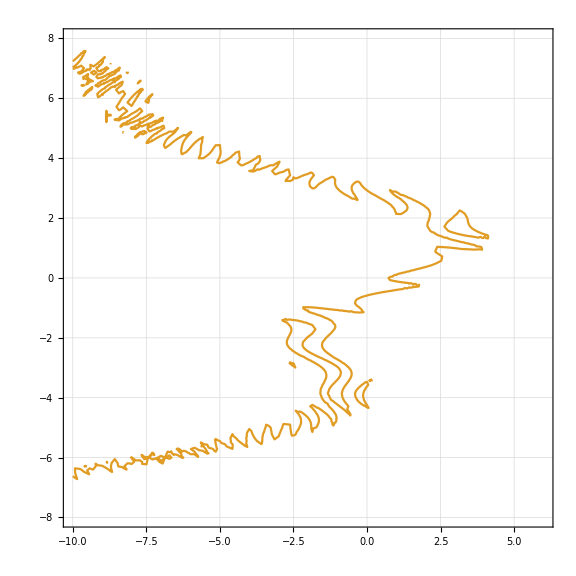

```mathematica
ContourPlot[{Red,expr//Evaluate}, {x,-10,6},{y,-8,8}, {AspectRatio->1, GridLines->Automatic, ImageSize->Large}]
```